```mathematica
Match1=Map[Style[#,Green]&,{Caroline<->Kato,Caroline<->Xari,Dieuw<->Kaat,Dieuw<->Sofia,Kaat<->Sofia,Kato<->Xari}]
```

{Caroline<->Kato,Caroline<->Xari,Dieuw<->Kaat,Dieuw<->Sofia,Kaat<->Sofia,Kato<->Xari}

```mathematica
Match2=Map[Style[#,Red]&,{Caroline<->Kaat,Caroline<->Kaat,Caroline<->Louise,Kaat<->Louise,Dieuw<->Kato,Xari<->Kato,Xari<->Dieuw,Xari<->Dieuw}];
```

```mathematica
Match3=Map[Style[#,Blue]&,{Xari<->Elise,Xari<->Kaat,Kaat<->Elise,Caroline<->Kato,Caroline<->Dieuw,Kato<->Dieuw}]
```

{Xari<->Elise,Xari<->Kaat,Kaat<->Elise,Caroline<->Kato,Caroline<->Dieuw,Kato<->Dieuw}

```mathematica
Match4=Map[Style[#,Darker[Yellow]]&,{Kaat<->Sofia,Kaat<->Kato,Sofia<->Kato,Caroline<->Dieuw,Caroline<->Elise,Elise<->Dieuw}]
```

{Kaat<->Sofia,Kaat<->Kato,Sofia<->Kato,Caroline<->Dieuw,Caroline<->Elise,Elise<->Dieuw}

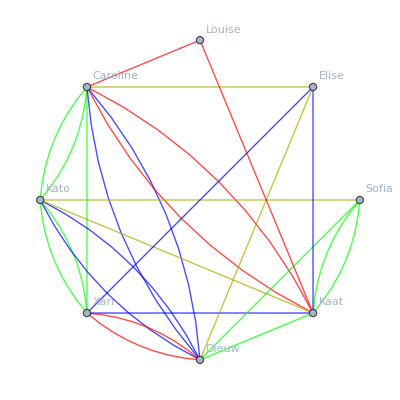

```mathematica
g=Graph[{Caroline,Kato,Xari,Dieuw,Kaat,Sofia,Elise,Louise},Join[Match1,Match2,Match3, Match4],
GraphLayout->"CircularEmbedding",
VertexLabels->"Name"
]
```

```mathematica
Length[DeleteDuplicates[Sort[Map[Sort[{#[[1]],#[[2]]}]&,EdgeList[VertexDelete [g,Louise]]]]]]
```

17

```mathematica
Sort[Map[Sort[{#[[1]],#[[2]]}]&,EdgeList[GraphComplement[EdgeList[VertexDelete [g,Louise]]]]]]
```

{{Caroline,Sofia},{Elise,Kato},{Elise,Sofia},{Sofia,Xari}}

```mathematica
EdgeCount[CompleteGraph[7]]
```

21